# Mathematica Supplement C: Strength of Selection and the existence of allele frequency limit cycles

Joint coevolutionary-epidemiological models dampen Red Queen cycles and alter conditions for epidemics, Ailene MacPherson and Sarah P. Otto, Theoretical Population Biology.

## Discrete-time SI model with sexual hosts and parasites

Morand et al. 1996 present a discrete-time SI model that exhibits allele frequency cycles.  Their model considers a diploid host that is castrated upon infection by its diploid pathogen. Castration implies strong selection on hosts susceptible to common pathogens, a condition that may favor the production of limit cycles.  Here we explore a similar model that allows partial castration and explore how the strength of selection in the form of fertility costs and virulence-induced mortality costs interact to produce allele frequency cycles.

We focus on a numerical analysis, using the parameters in the Morand et al. model that allowed for cycles in allele frequencies in hosts and parasites, to determine the required strength of selection that would allow cycling.

The difference equations

Let s[h,t] be the number of susceptible hosts of genotype h at time t and i[h,p,t] the number of infected hosts of type h infected with pathogen of genotype p. Here h and p range from 1 to 3 representing a diploid genotype at a single locus. Hosts and pathogens produce sexually with all offspring entering the susceptible class.  If we let n be a vector of length 3 giving the number of viable parents of each genotype, the number of offspring of type j produced by random mating is given by:

```mathematica
m[n_,j_]:=Block[{offVec,out,ntot},ntot=Total[n];
offVec={{n[[1]]/ntot+1/2 n[[2]]/ntot,1/2 n[[1]]/ntot+1/4 n[[2]]/ntot,0},{1/2 n[[2]]/ntot+n[[3]]/ntot,1/2 n[[1]]/ntot+1/2 n[[2]]/ntot+1/2 n[[3]]/ntot,n[[1]]/ntot+1/2 n[[2]]/ntot},{0,1/4 n[[2]]/ntot+1/2 n[[3]]/ntot,1/2 n[[2]]/ntot+n[[3]]/ntot}}.{n[[1]],n[[2]],n[[3]]};  
out=offVec[[j]]]
```

```mathematica
(*(m[n,1]+m[n,2]+m[n,3]//Simplify)/Total[n]*)
```

Letting s[h,t+Δt]=f1[h,t] and i[h,p,t+Δt]=f2[h,p,t]

```mathematica
lm={{1,0,0},{0,1,0},{0,0,1}};
f1[h_,t_]:=s[h,t]+r Δt(1-κ (Sum[s[k,t]+Sum[i[k,p,t],{p,1,3}],{k,1,3}])) m[Table[s[k,t]+ρ Sum[i[k,p,t],{p,1,3}],{k,1,3}],h]-β Δt s[h,t]Sum[lm[[h,l]] m[Table[Sum[i[k,l2,t],{k,1,3}],{l2,1,3}],l],{l,1,3}]
f2[h_,p_,t_]:=i[h,p,t]+β Δt s[h,t]lm[[h,p]] m[Table[Sum[i[k,l2,t],{k,1,3}],{l2,1,3}],p]-μ Δt i[h,p,t]
```

Here r is the growth rate, κ is the inverse of the carrying capacity, ρ is the fertility of infected hosts with 0 being complete castration and 1 being no fertility cost, β is the transmission rate, and μ is the virulent death rate of infected hosts. Finally, Δt gives the length of a discrete time step, here set to one.

Numerical Analysis

```mathematica
pars={r->0.2,κ->1/2000,ρ->1,β->0.0002,μ->0.05,Δt->1,tmax->5000};
```

## The equilibria

```mathematica
equs=Join[Table[f1[h,t]==s[h,t],{h,1,3}],Flatten[Table[f2[h,p,t]==i[h,p,t],{h,1,3},{p,1,3}]]];
vars=Join[Table[s[h,t],{h,1,3}],Flatten[Table[i[h,p,t],{h,1,3},{p,1,3}]]];
```

Identifying the equilibria with disease present:

```mathematica
nEqu[Pars_]:=Block[{nsol,out},
nsol=Solve[equs/.Pars,vars]//Quiet;
out=Select[nsol,(s[1,t]/.#)>0&&(s[2,t]/.#)>0&&(s[3,t]/.#)>0&&(i[1,1,t]/.#)>0&]//Flatten
]
```

```mathematica
nEqu[pars]
```

{s[1,t]→500.,s[2,t]→500.,s[3,t]→500.,i[1,1,t]→80.7189,i[1,2,t]→0.,i[1,3,t]→0.,i[2,1,t]→0.,i[2,2,t]→161.438,i[2,3,t]→0.,i[3,1,t]→0.,i[3,2,t]→0.,i[3,3,t]→80.7189}

## Numerical Simulation

### Numerical Iteration

Numerical iteration as a function of parameter combination

```mathematica
nIterate[Pars_]:=Block[{F1,F2,ssol,isol,nsol,out,equ},
Clear[F1,F2,ssol,isol,nsol];
(*The equations*)
lm={{1,0,0},{0,1,0},{0,0,1}};
F1[h_,t_]:=ssol[h,t]+r Δt(1-κ (Sum[ssol[k,t]+Sum[isol[k,p,t],{p,1,3}],{k,1,3}])) m[Table[ssol[k,t]+ρ Sum[isol[k,p,t],{p,1,3}],{k,1,3}],h]-β Δt ssol[h,t]Sum[lm[[h,l]] m[Table[Sum[isol[k,l2,t],{k,1,3}],{l2,1,3}],l],{l,1,3}];
F2[h_,p_,t_]:=isol[h,p,t]+β Δt ssol[h,t]lm[[h,p]] m[Table[Sum[isol[k,l2,t],{k,1,3}],{l2,1,3}],p]-μ Δt isol[h,p,t];
ssol[h_,t_]:=ssol[h,t]=F1[h,t-1]/.Pars;
isol[h_,p_,t_]:=isol[h,p,t]=F2[h,p,t-1]/.Pars;
(*Inital conditions*)
equ=nEqu[Pars];
ssol[h_,0]:=ssol[h,0]=0.9^h s[h,t]/.equ;
isol[h_,p_,0]:=isol[h,p,0]=0.9^h i[h,p,t]/.equ;
Join[Table[ssol[h,0],{h,1,3}],Flatten[Table[isol[h,p,0],{h,1,3},{p,1,3}]]];
(*Itterating*)
out=Table[Join[Table[ssol[h,t],{h,1,3}],Flatten[Table[isol[h,p,t],{h,1,3},{p,1,3}]]],{t,0,tmax/.Pars}]
]
```

```mathematica
Clear[ssol,isol,nsol]
```

```mathematica
nsol=nIterate[pars];
ssol[h_,t_]:=nsol[[t+1,h]]
isol[h_,p_,t_]:=nsol[[t+1,3+3(h-1)+p]]
```

### Plotting

#### Epidemiological dynamics

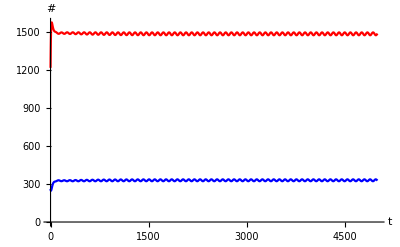

```mathematica
ListLinePlot[{Table[{t,Sum[ssol[h,t],{h,1,3}]},{t,0,tmax/.pars}],Table[{t,Sum[isol[h,p,t],{h,1,3},{p,1,3}]},{t,0,tmax/.pars}]},PlotStyle->{Red,Blue},AxesLabel->{"t","#"}]
```

#### Allele Frequency dynamics

Plotted over time

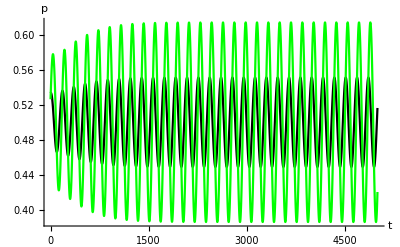

```mathematica
ListLinePlot[{Table[{t,(ssol[1,t]+1/2 ssol[2,t]+Sum[isol[1,p,t]+1/2 isol[2,p,t],{p,1,3}])/Sum[ssol[k,t]+Sum[isol[k,l,t],{l,1,3}],{k,1,3}]},{t,0,tmax/.pars}],Table[{t,Sum[isol[1,p,t]+1/2 isol[2,p,t],{p,1,3}]/Sum[isol[k,l,t],{l,1,3},{k,1,3}]},{t,0,tmax/.pars}]},PlotStyle->{Black,Green},PlotRange->All,AxesLabel->{"t","p"}]
```

Plotted in phase space (starting condition shown as a red point): (starting condition shown as a red point)

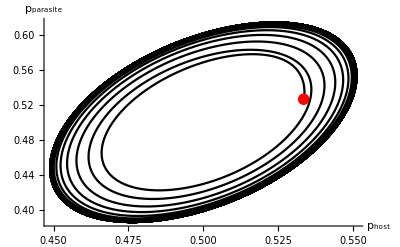

```mathematica
Show[
ListLinePlot[{Table[{(ssol[1,t]+1/2 ssol[2,t]+Sum[isol[1,p,t]+1/2 isol[2,p,t],{p,1,3}])/Sum[ssol[k,t]+Sum[isol[k,l,t],{l,1,3}],{k,1,3}],Sum[isol[1,p,t]+1/2 isol[2,p,t],{p,1,3}]/Sum[isol[k,l,t],{l,1,3},{k,1,3}]},{t,0,tmax/.pars}]},PlotStyle->{Black},PlotRange->All,AxesLabel->{"p_host","p_parasite"}],
ListPlot[{{(ssol[1,0]+1/2 ssol[2,0]+Sum[isol[1,p,0]+1/2 isol[2,p,0],{p,1,3}])/Sum[ssol[k,0]+Sum[isol[k,l,0],{l,1,3}],{k,1,3}],Sum[isol[1,p,0]+1/2 isol[2,p,0],{p,1,3}]/Sum[isol[k,l,0],{l,1,3},{k,1,3}]}/.pars},PlotStyle->{PointSize[0.02],Red}]]
```

## Numerical stability

### Jacobian matrix

```mathematica
nJmtrx[Pars_]:=Block[{jmtrx,out,h1,h2,p1,p2,row},jmtrx=Table[{},{row,1,12}];
For[h1=1,h1≤3,h1++,row=h1;
For[h2=1,h2≤3,h2++,
AppendTo[jmtrx[[row]],D[f1[h1,t],s[h2,t]]]
];
For[h2=1,h2≤3,h2++,
For[p2=1,p2≤3,p2++,
AppendTo[jmtrx[[row]],D[f1[h1,t],i[h2,p2,t]]]
];
];
];
For[h1=1,h1≤3,h1++,
For[p1=1,p1≤3,p1++,row=3+3(h1-1)+p1;
For[h2=1,h2≤3,h2++,
AppendTo[jmtrx[[row]],D[f2[h1,p1,t],s[h2,t]]];
];
For[h2=1,h2≤3,h2++,
For[p2=1,p2≤3,p2++,
AppendTo[jmtrx[[row]],D[f2[h1,p1,t],i[h2,p2,t]]]
];
];
];
];
jmtrx/.Pars/.nEqu[Pars]
]
```

```mathematica
Eigenvalues[nJmtrx[pars]]
```

{1.00078+0.0364392 ⅈ,1.00078-0.0364392 ⅈ,0.980848+0. ⅈ,0.949915+0. ⅈ,0.9+0. ⅈ,0.9+0. ⅈ,0.9+0. ⅈ,0.9+0. ⅈ,0.9+0. ⅈ,0.9+0. ⅈ,0.9+0. ⅈ,0.856231+0. ⅈ}

### Stability function

```mathematica
stab[Pars_]:=Block[{λs,mag,out},
If[Length[nEqu[Pars]]<1,out=0 (*No endemic equilibrium*),
λs=Eigenvalues[nJmtrx[Pars]];
mag=Sqrt[Re[λs]^2+Im[λs]^2];
If[Max[Im[λs]]>0,
(*Cycles*)If[Max[mag]>1,(*unstable*)out=3,(*stable*)out=2],
(*No cycles*)out=1] 
];
out
]
```

### Stability across parameter space

Here we explore the stability of the system as a function of infected the fertility upon infection, ρ, and virulence μ focusing solely on the disease-present equilibrium.

```mathematica
parsSub={r->0.2,κ->1/2000,β->0.0002,Δt->1};
```

```mathematica
tab1=Table[{x,10^y,stab[Join[parsSub,{ρ->x,μ->10^y}]]},{x,0,1,0.2},{y,-6,-1,1}];
```

$Aborted

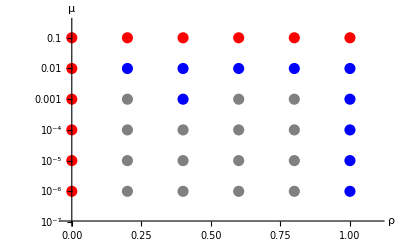

```mathematica
ListLogPlot[{Join[Select[Flatten[tab1,1],#[[3]]==0&][[;;,{1,2}]],{{-100,-100}}],Join[Select[Flatten[tab1,1],#[[3]]==1&][[;;,{1,2}]],{{-100,-100}}],
Join[Select[Flatten[tab1,1],#[[3]]==2&][[;;,{1,2}]],{{-100,-100}}],
Join[Select[Flatten[tab1,1],#[[3]]==3&][[;;,{1,2}]],{{-100,-100}}]},PlotRange->{{-0.02,1.1},{10^-7,10^-0.5}},AxesLabel->{"ρ","μ"},PlotStyle-> {{PointSize[0.02],Black},{PointSize[0.02],Gray},{PointSize[0.02],Blue},{PointSize[0.02],Red}}]
```

Black = no equilibrium with disease present
Gray = No cycles
Blue = Stable endemic equilibrium with cycles. Damped allele-frequency cycles.
Red = Unstable endemic equilibrium with cycles. Possible allele-frequency limit cycles.

Plotting ρ and μ on a log scales and focusing on parameters with high levels of castration (ρ near zero) and high virulence (large μ):

```mathematica
tab2=Table[{10^x,10^y,stab[Join[parsSub,{ρ->10^x,μ->10^y}]]},{x,-4,Log10[0.3],0.2},{y,-3,-0.5,0.5}];
```

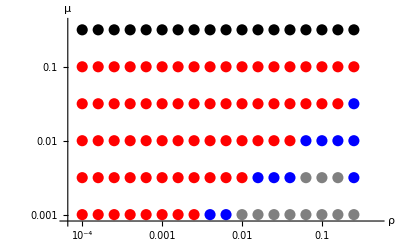

```mathematica
ListLogLogPlot[{Join[Select[Flatten[tab2,1],#[[3]]==0&][[;;,{1,2}]],{{-100,-100}}],Join[Select[Flatten[tab2,1],#[[3]]==1&][[;;,{1,2}]],{{-100,-100}}],
Join[Select[Flatten[tab2,1],#[[3]]==2&][[;;,{1,2}]],{{-100,-100}}],
Join[Select[Flatten[tab2,1],#[[3]]==3&][[;;,{1,2}]],{{-100,-100}}]},PlotRange->{{10^-4.2,0.5},{10^-3.1,10^-0.4}},AxesLabel->{"ρ","μ"},PlotStyle-> {{PointSize[0.02],Black},{PointSize[0.02],Gray},{PointSize[0.02],Blue},{PointSize[0.02],Red}}]
```

Black = No equilibrium with disease present
Gray = No cycles (leading eigenvalue is real)
Blue = Stable endemic equilibrium with damped cycles. Allele-frequency cycles, if present, dissipate.
Red = Unstable equilibrium with cycles. Possible allele-frequency limit cycles.

### Checking for allele frequency cycles

In the previous section red points denoted parameter combinations with a leading positive complex eigenvalue and hence possible exhibit allele frequency limit cycles.  Here we assess whether these points do likely have allele frequency limit or stable cycles by calculating whether the variance in allele frequency increases or decreases over time.

```mathematica
AFstab[ρμPt_]:=Block[{j,ρ,μ,Pars,vH1,vH2,vP1,vP2,out}, 
Clear[ssol,isol];
Pars=Join[parsSub,{ρ->ρμPt[[1]], μ->ρμPt[[2]],tmax->5000 }];out={};
nsol=nIterate[Pars];
ssol[h_,t_]:=nsol[[t+1,h]];
isol[h_,p_,t_]:=nsol[[t+1,3+3(h-1)+p]];
(*Comparing variance between interval t=[0,1000] vs. interval t=[4000,5000]*)
vH1=Variance[Table[(ssol[1,t]+1/2 ssol[2,t]+Sum[isol[1,p,t]+1/2 isol[2,p,t],{p,1,3}])/Sum[ssol[k,t]+Sum[isol[k,l,t],{l,1,3}],{k,1,3}],{t,0,1000}]];
vH2=Variance[Table[(ssol[1,t]+1/2 ssol[2,t]+Sum[isol[1,p,t]+1/2 isol[2,p,t],{p,1,3}])/Sum[ssol[k,t]+Sum[isol[k,l,t],{l,1,3}],{k,1,3}],{t,4000,5000}]];
vP1=Variance[Table[Sum[isol[1,p,t]+1/2 isol[2,p,t],{p,1,3}]/Sum[isol[k,l,t],{l,1,3},{k,1,3}],{t,0,1000}]];
vP2=Variance[Table[Sum[isol[1,p,t]+1/2 isol[2,p,t],{p,1,3}]/Sum[isol[k,l,t],{l,1,3},{k,1,3}],{t,4000,5000}]];
If[vH1>vH2,
(*host stable*)
If[vP1>vP2,(*parasite stable*)out={1,vH2-vH1,vP2-vP1},(*parasite unstable=Error*) out={3,vH2-vH1,vP2-vP1}],
(*host unstable*)
If[vP1>vP2,(*parasite stable=Error*)out={3,vH2-vH1,vP2-vP1},(*parasite unstable*) out={2,vH2-vH1,vP2-vP1}]];
out
]
```

If AFstab={1,-,-} then stable allele frequency cycles
If AFstab={2,+,+} then unstable allele frequency cycles
If AFstab={3,+,-} or {3,-,+} then host and parasite variance trends do not agree. Possible problem with length of intervals relative to period of cycles.

For each red point in tab2 are there likely allele frequency cycles?

```mathematica
Module[{j,Pts},Cycles2={};
Pts=Select[Flatten[tab2,1],#[[3]]==3&][[;;,{1,2}]];
For[j=1,j≤Length[Pts],j++,
AppendTo[Cycles2,Join[Pts[[j]],{AFstab[Pts[[j]]]}]]
];
]
```

```mathematica
Cycles2
```

{{0.0001,0.001,2},{0.0001,0.00316228,2},{0.0001,0.01,2},{0.0001,0.0316228,2},{0.0001,0.1,2},{0.000158489,0.001,2},{0.000158489,0.00316228,2},{0.000158489,0.01,2},{0.000158489,0.0316228,2},{0.000158489,0.1,2},{0.000251189,0.001,2},{0.000251189,0.00316228,2},{0.000251189,0.01,2},{0.000251189,0.0316228,2},{0.000251189,0.1,2},{0.000398107,0.001,2},{0.000398107,0.00316228,2},{0.000398107,0.01,2},{0.000398107,0.0316228,2},{0.000398107,0.1,2},{0.000630957,0.001,2},{0.000630957,0.00316228,2},{0.000630957,0.01,2},{0.000630957,0.0316228,2},{0.000630957,0.1,2},{0.001,0.001,2},{0.001,0.00316228,2},{0.001,0.01,2},{0.001,0.0316228,2},{0.001,0.1,2},{0.00158489,0.001,2},{0.00158489,0.00316228,2},{0.00158489,0.01,2},{0.00158489,0.0316228,2},{0.00158489,0.1,2},{0.00251189,0.001,2},{0.00251189,0.00316228,2},{0.00251189,0.01,2},{0.00251189,0.0316228,2},{0.00251189,0.1,2},{0.00398107,0.00316228,2},{0.00398107,0.01,2},{0.00398107,0.0316228,2},{0.00398107,0.1,2},{0.00630957,0.00316228,2},{0.00630957,0.01,2},{0.00630957,0.0316228,2},{0.00630957,0.1,2},{0.01,0.00316228,2},{0.01,0.01,2},{0.01,0.0316228,2},{0.01,0.1,2},{0.0158489,0.01,2},{0.0158489,0.0316228,2},{0.0158489,0.1,2},{0.0251189,0.01,2},{0.0251189,0.0316228,2},{0.0251189,0.1,2},{0.0398107,0.01,2},{0.0398107,0.0316228,2},{0.0398107,0.1,2},{0.0630957,0.0316228,2},{0.0630957,0.1,2},{0.1,0.0316228,2},{0.1,0.1,2},{0.158489,0.0316228,2},{0.158489,0.1,2},{0.251189,0.1,2}}

All red points appear to have allele frequency limit cycles.

Conclusion: The disease-present equilibrium is unstable, with perturbations cycling outwards, only when the disease reduces fertility severely (ρ near 0) or has a high mortality cost (μ high) or both.

## Continuous-time SI model with sexual hosts and parasites

This section is identical to that above (and the Morand et al. model) except that its analyzed in continuous time.

The differential equations

Let s[h,t] be the number of susceptible hosts of genotype h at time t and i[h,p,t] the number of infected hosts of type h infected with pathogen of genotype p. Here h and p range from 1 to 3 representing a diploid genotype at a single locus. Hosts and pathogens produce sexually with all offspring entering the susceptible class.  If we let n be a vector of length 3 giving the number of viable parents of each genotype the number of offspring of type j produced by random mating is given by:

```mathematica
m[n_,j_]:=Block[{offVec,out,ntot},ntot=Total[n];
offVec={{n[[1]]/ntot+1/2 n[[2]]/ntot,1/2 n[[1]]/ntot+1/4 n[[2]]/ntot,0},{1/2 n[[2]]/ntot+n[[3]]/ntot,1/2 n[[1]]/ntot+1/2 n[[2]]/ntot+1/2 n[[3]]/ntot,n[[1]]/ntot+1/2 n[[2]]/ntot},{0,1/4 n[[2]]/ntot+1/2 n[[3]]/ntot,1/2 n[[2]]/ntot+n[[3]]/ntot}}.{n[[1]],n[[2]],n[[3]]};  
out=offVec[[j]]]
```

```mathematica
(*(m[n,1]+m[n,2]+m[n,3]//Simplify)/Total[n]*)
```

Letting ds[h,t]/dt=g1[h,t] and di[h,p,t]/dt=g2[h,p,t]

```mathematica
lm={{1,0,0},{0,1,0},{0,0,1}};
g1[h_,t_]:=r(1-κ (Sum[s[k,t]+Sum[i[k,p,t],{p,1,3}],{k,1,3}])) m[Table[s[k,t]+ρ Sum[i[k,p,t],{p,1,3}],{k,1,3}],h]-β s[h,t]Sum[lm[[h,l]] m[Table[Sum[i[k,l2,t],{k,1,3}],{l2,1,3}],l],{l,1,3}]
g2[h_,p_,t_]:=β s[h,t]lm[[h,p]] m[Table[Sum[i[k,l2,t],{k,1,3}],{l2,1,3}],p]-μ i[h,p,t]
```

Here r is the growth rate, κ is the inverse of the carrying capacity, ρ is the fertility of infected hosts with 0 being complete castration and 1 being no fertility cost, β is the transmission rate, and μ is the virulent death rate of infected hosts.

Numerical Analysis

```mathematica
pars={r->0.2,κ->1/2000,ρ->0,β->0.0002,μ->0.1,tmax->5000};
```

## The equilibria

```mathematica
equs=Join[Table[g1[h,t]==0,{h,1,3}],Flatten[Table[g2[h,p,t]==0,{h,1,3},{p,1,3}]]];
vars=Join[Table[s[h,t],{h,1,3}],Flatten[Table[i[h,p,t],{h,1,3},{p,1,3}]]];
```

```mathematica
nEqu[Pars_]:=Block[{nsol,out},
nsol=Solve[equs/.Pars,vars]//Quiet;
out=Select[nsol,(s[1,t]/.#)>0&&(s[2,t]/.#)>0&&(s[3,t]/.#)>0&&(i[1,1,t]/.#)>0&]//Flatten
]
```

```mathematica
nEqu[pars]
```

{s[1,t]→250.,s[2,t]→250.,s[3,t]→250.,i[1,1,t]→242.061,i[1,2,t]→0.,i[1,3,t]→0.,i[2,1,t]→0.,i[2,2,t]→484.123,i[2,3,t]→0.,i[3,1,t]→0.,i[3,2,t]→0.,i[3,3,t]→242.061}

## Numerical Simulation

### Numerical Iteration

Numerical iteration as a function of parameter combination

```mathematica
nIterate[Pars_]:=Block[{ODEs,vars,ssol,isol,nsol,out,equ},
Clear[ssol,isol,nsol];
(*The equations*)
ODEs=Join[Table[D[s[h,t],t]==g1[h,t],{h,1,3}],Flatten[Table[D[i[h,p,t],t]==g2[h,p,t],{h,1,3},{p,1,3}]]];
vars=Join[Table[s[h,t],{h,1,3}],Flatten[Table[i[h,p,t],{h,1,3},{p,1,3}]]];
(*Inital conditions*)
equ=nEqu[Pars];
inits=Join[Table[s[h,0]==0.9^h s[h,t]/.equ,{h,1,3}],Flatten[Table[i[h,p,0]==0.9^h i[h,p,t]/.equ,{h,1,3},{p,1,3}]]];
(*Itterating*)
out=NDSolve[Join[ODEs/.Pars,inits],vars,{t,0,tmax/.Pars}]//Flatten
]
```

```mathematica
Clear[ssol,isol,nsol]
```

```mathematica
nsol=nIterate[pars];
ssol[h_,τ_]:=s[h,t]/.nsol/.{t->τ}
isol[h_,p_,τ_]:=i[h,p,t]/.nsol/.{t->τ}
```

### Plotting

#### Epidemiological dynamics

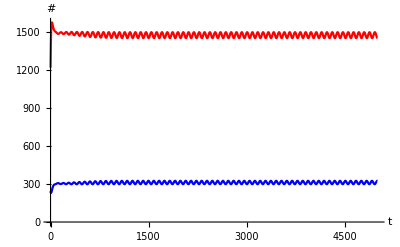

```mathematica
ListLinePlot[{Table[{t,Sum[ssol[h,t],{h,1,3}]},{t,0,tmax/.pars}],Table[{t,Sum[isol[h,p,t],{h,1,3},{p,1,3}]},{t,0,tmax/.pars}]},PlotStyle->{Red,Blue},AxesLabel->{"t","#"}]
```

#### Allele Frequency dynamics

Plotted over time

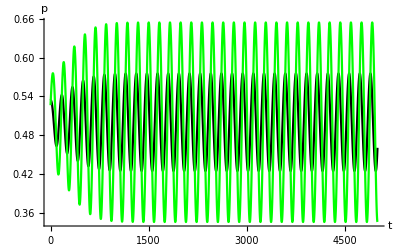

```mathematica
ListLinePlot[{Table[{t,(ssol[1,t]+1/2 ssol[2,t]+Sum[isol[1,p,t]+1/2 isol[2,p,t],{p,1,3}])/Sum[ssol[k,t]+Sum[isol[k,l,t],{l,1,3}],{k,1,3}]},{t,0,tmax/.pars}],Table[{t,Sum[isol[1,p,t]+1/2 isol[2,p,t],{p,1,3}]/Sum[isol[k,l,t],{l,1,3},{k,1,3}]},{t,0,tmax/.pars}]},PlotStyle->{Black,Green},PlotRange->All,AxesLabel->{"t","p"}]
```

Plotted in phase space (starting condition shown as a red point):

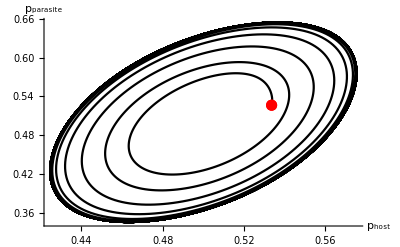

```mathematica
Show[ListLinePlot[{Table[{(ssol[1,t]+1/2 ssol[2,t]+Sum[isol[1,p,t]+1/2 isol[2,p,t],{p,1,3}])/Sum[ssol[k,t]+Sum[isol[k,l,t],{l,1,3}],{k,1,3}],Sum[isol[1,p,t]+1/2 isol[2,p,t],{p,1,3}]/Sum[isol[k,l,t],{l,1,3},{k,1,3}]},{t,0,tmax/.pars}]},PlotStyle->{Black},PlotRange->All,AxesLabel->{"p_host","p_parasite"}],
ListPlot[{{(ssol[1,0]+1/2 ssol[2,0]+Sum[isol[1,p,0]+1/2 isol[2,p,0],{p,1,3}])/Sum[ssol[k,0]+Sum[isol[k,l,0],{l,1,3}],{k,1,3}],Sum[isol[1,p,0]+1/2 isol[2,p,0],{p,1,3}]/Sum[isol[k,l,0],{l,1,3},{k,1,3}]}/.pars},PlotStyle->{PointSize[0.02],Red}]
]
```

## Numerical stability

### Jacobian matrix

```mathematica
nJmtrx[Pars_]:=Block[{jmtrx,out,h1,h2,p1,p2,row},jmtrx=Table[{},{row,1,12}];
For[h1=1,h1≤3,h1++,row=h1;
For[h2=1,h2≤3,h2++,
AppendTo[jmtrx[[row]],D[g1[h1,t],s[h2,t]]]
];
For[h2=1,h2≤3,h2++,
For[p2=1,p2≤3,p2++,
AppendTo[jmtrx[[row]],D[g1[h1,t],i[h2,p2,t]]]
];
];
];
For[h1=1,h1≤3,h1++,
For[p1=1,p1≤3,p1++,row=3+3(h1-1)+p1;
For[h2=1,h2≤3,h2++,
AppendTo[jmtrx[[row]],D[g2[h1,p1,t],s[h2,t]]];
];
For[h2=1,h2≤3,h2++,
For[p2=1,p2≤3,p2++,
AppendTo[jmtrx[[row]],D[g2[h1,p1,t],i[h2,p2,t]]]
];
];
];
];
jmtrx/.Pars/.nEqu[Pars]
]
```

```mathematica
Eigenvalues[nJmtrx[pars]]
```

{-0.116127+0.0504289 ⅈ,-0.116127-0.0504289 ⅈ,-0.0566321+0. ⅈ,-0.05+0. ⅈ,-0.05+0. ⅈ,-0.05+0. ⅈ,-0.05+0. ⅈ,-0.05+0. ⅈ,-0.05+0. ⅈ,-0.05+0. ⅈ,-0.0101184+0.0308901 ⅈ,-0.0101184-0.0308901 ⅈ}

### Stability function

```mathematica
stab[Pars_]:=Block[{λs,mag,out},
If[Length[nEqu[Pars]]<1,out=0 (*No endemic equilibrium*),
λs=Eigenvalues[nJmtrx[Pars]];
If[Max[Im[λs]]>0,
(*Cycles*)If[Max[Re[λs]]>0,(*unstable*)out=3,(*stable*)out=2],
(*No cycles*)out=1] 
];
out
]
```

### Stability across parameter space

Here we explore the stability of the system as a function of the fertility upon infection, ρ, and virulence, μ, focusing solely on the disease-present equilibrium.

```mathematica
parsSub={r->0.2,κ->1/2000,β->0.0002};
```

```mathematica
tab1=Table[{x,10^y,stab[Join[parsSub,{ρ->x,μ->10^y}]]},{x,0,1,0.2},{y,-6,-1,1}];
```

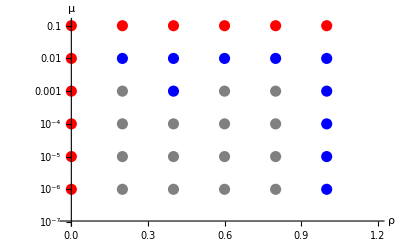

```mathematica
ListLogPlot[{Join[Select[Flatten[tab1,1],#[[3]]==0&][[;;,{1,2}]],{{-100,-100}}],Join[Select[Flatten[tab1,1],#[[3]]==1&][[;;,{1,2}]],{{-100,-100}}],
Join[Select[Flatten[tab1,1],#[[3]]==2&][[;;,{1,2}]],{{-100,-100}}],
Join[Select[Flatten[tab1,1],#[[3]]==3&][[;;,{1,2}]],{{-100,-100}}]},PlotRange->{{-0.02,1.2},{10^-7,10^-0.9}},AxesLabel->{"ρ","μ"},PlotStyle-> {{PointSize[0.02],Black},{PointSize[0.02],Gray},{PointSize[0.02],Blue},{PointSize[0.02],Red}}]
```

Black = No equilibrium with disease present
Gray = No cycles (leading eigenvalue is real)
Blue = Stable endemic equilibrium with damped cycles. Allele-frequency cycles, if present, dissipate.
Red = Unstable equilibrium with cycles. Possible allele-frequency limit cycles.

Plotting ρ on a log scale to focus on parameters with high levels of castration (ρ near zero):

```mathematica
tab2=Table[{10^x,10^y,stab[Join[parsSub,{ρ->10^x,μ->10^y}]]},{x,-4,Log10[0.3],0.2},{y,-3,-0.5,0.5}];
```

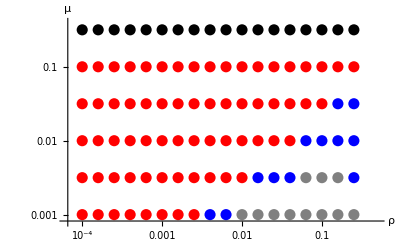

```mathematica
ListLogLogPlot[{Join[Select[Flatten[tab2,1],#[[3]]==0&][[;;,{1,2}]],{{-100,-100}}],Join[Select[Flatten[tab2,1],#[[3]]==1&][[;;,{1,2}]],{{-100,-100}}],
Join[Select[Flatten[tab2,1],#[[3]]==2&][[;;,{1,2}]],{{-100,-100}}],
Join[Select[Flatten[tab2,1],#[[3]]==3&][[;;,{1,2}]],{{-100,-100}}]},PlotRange->{{10^-4.2,0.5},{10^-3.1,10^-0.4}},AxesLabel->{"ρ","μ"},PlotStyle-> {{PointSize[0.02],Black},{PointSize[0.02],Gray},{PointSize[0.02],Blue},{PointSize[0.02],Red}}]
```

Black = No equilibrium with disease present
Gray = No cycles (leading eigenvalue is real)
Blue = Stable endemic equilibrium with damped cycles. Allele-frequency cycles, if present, dissipate.
Red = Unstable equilibrium with cycles. Possible allele-frequency limit cycles.

### Checking for allele frequency cycles

Once again checking red points for allele frequency limit cycles.

```mathematica
AFstab[ρμPt_]:=Block[{j,ρ,μ,Pars,vH1,vH2,vP1,vP2,out}, 
Clear[ssol,isol];
Pars=Join[parsSub,{ρ->ρμPt[[1]], μ->ρμPt[[2]],tmax->5000 }];out={};
nsol=nIterate[pars];
ssol[h_,τ_]:=s[h,t]/.nsol/.{t->τ};
isol[h_,p_,τ_]:=i[h,p,t]/.nsol/.{t->τ};
(*Comparing variance between interval t=[0,1000] vs. interval t=[4000,5000]*)
vH1=Variance[Table[(ssol[1,t]+1/2 ssol[2,t]+Sum[isol[1,p,t]+1/2 isol[2,p,t],{p,1,3}])/Sum[ssol[k,t]+Sum[isol[k,l,t],{l,1,3}],{k,1,3}],{t,0,1000}]];
vH2=Variance[Table[(ssol[1,t]+1/2 ssol[2,t]+Sum[isol[1,p,t]+1/2 isol[2,p,t],{p,1,3}])/Sum[ssol[k,t]+Sum[isol[k,l,t],{l,1,3}],{k,1,3}],{t,4000,5000}]];
vP1=Variance[Table[Sum[isol[1,p,t]+1/2 isol[2,p,t],{p,1,3}]/Sum[isol[k,l,t],{l,1,3},{k,1,3}],{t,0,1000}]];
vP2=Variance[Table[Sum[isol[1,p,t]+1/2 isol[2,p,t],{p,1,3}]/Sum[isol[k,l,t],{l,1,3},{k,1,3}],{t,4000,5000}]];
If[vH1>vH2,
(*host stable*)
If[vP1>vP2,(*parasite stable*)out={1,vH2-vH1,vP2-vP1},(*parasite unstable=Error*) out={3,vH2-vH1,vP2-vP1}],
(*host unstable*)
If[vP1>vP2,(*parasite stable=Error*)out={3,vH2-vH1,vP2-vP1},(*parasite unstable*) out={2,vH2-vH1,vP2-vP1}]];
out
]
```

If AFstab={1,-,-} then stable allele frequency cycles
If AFstab={2,+,+} then unstable allele frequency cycles
If AFstab={3,+,-} or {3,-,+} then host and parasite variance trends do not agree. Possible problem with length of intervals relative to period of cycles.

For each red point in tab2 are there likely allele frequency cycles?

```mathematica
Module[{j,Pts},Cycles2={};
Pts=Select[Flatten[tab2,1],#[[3]]==3&][[;;,{1,2}]];
For[j=1,j≤Length[Pts],j++,
AppendTo[Cycles2,Join[Pts[[j]],{AFstab[Pts[[j]]]}]]
];
]
```

```mathematica
Cycles2
```

{{0.0001,0.001,2},{0.0001,0.00316228,2},{0.0001,0.01,2},{0.0001,0.0316228,2},{0.0001,0.1,2},{0.000158489,0.001,2},{0.000158489,0.00316228,2},{0.000158489,0.01,2},{0.000158489,0.0316228,2},{0.000158489,0.1,2},{0.000251189,0.001,2},{0.000251189,0.00316228,2},{0.000251189,0.01,2},{0.000251189,0.0316228,2},{0.000251189,0.1,2},{0.000398107,0.001,2},{0.000398107,0.00316228,2},{0.000398107,0.01,2},{0.000398107,0.0316228,2},{0.000398107,0.1,2},{0.000630957,0.001,2},{0.000630957,0.00316228,2},{0.000630957,0.01,2},{0.000630957,0.0316228,2},{0.000630957,0.1,2},{0.001,0.001,2},{0.001,0.00316228,2},{0.001,0.01,2},{0.001,0.0316228,2},{0.001,0.1,2},{0.00158489,0.001,2},{0.00158489,0.00316228,2},{0.00158489,0.01,2},{0.00158489,0.0316228,2},{0.00158489,0.1,2},{0.00251189,0.001,2},{0.00251189,0.00316228,2},{0.00251189,0.01,2},{0.00251189,0.0316228,2},{0.00251189,0.1,2},{0.00398107,0.00316228,2},{0.00398107,0.01,2},{0.00398107,0.0316228,2},{0.00398107,0.1,2},{0.00630957,0.00316228,2},{0.00630957,0.01,2},{0.00630957,0.0316228,2},{0.00630957,0.1,2},{0.01,0.00316228,2},{0.01,0.01,2},{0.01,0.0316228,2},{0.01,0.1,2},{0.0158489,0.01,2},{0.0158489,0.0316228,2},{0.0158489,0.1,2},{0.0251189,0.01,2},{0.0251189,0.0316228,2},{0.0251189,0.1,2},{0.0398107,0.01,2},{0.0398107,0.0316228,2},{0.0398107,0.1,2},{0.0630957,0.0316228,2},{0.0630957,0.1,2},{0.1,0.0316228,2},{0.1,0.1,2},{0.158489,0.1,2},{0.251189,0.1,2}}

All red points appear to have allele frequency limit cycles.

Conclusion: The disease-present equilibrium is unstable, with perturbations cycling outwards, only when the disease reduces fertility severely (ρ near 0) or has a high mortality cost (μ high) or both.

## Discrete-time SI model with asexual hosts and parasites

Similar model but with asexual hosts and parasites.

The difference equations

Let s[h,t] be the number of susceptible hosts of genotype h at time t and i[h,p,t] the number of infected hosts of type h infected with pathogen of genotype p. Here h and p range from 1 to 3 representing a diploid genotype at a single locus. Hosts and pathogens produce sexually with all offspring entering the susceptible class.  If we let n be a vector of length 3 giving the number of viable parents of each genotype the number of offspring of type j produced by random mating is given by:

```mathematica
(*(m[n,1]+m[n,2]+m[n,3]//Simplify)/Total[n]*)
```

Letting s[h,t+Δt]=f1[h,t] and i[h,p,t+Δt]=f2[h,p,t]

```mathematica
Clear[f1,f2]
```

```mathematica
lm={{1,0,0},{0,1,0},{0,0,1}};
f1[h_,t_]:=s[h,t]+r Δt(1-κ (Sum[s[k,t]+Sum[i[k,p,t],{p,1,3}],{k,1,3}]))(s[h,t]+ρ Sum[i[h,p,t],{p,1,3}])-β Δt s[h,t]Sum[lm[[h,l]] i[k,l,t],{k,1,3},{l,1,3}]
f2[h_,p_,t_]:=i[h,p,t]+β Δt s[h,t]lm[[h,p]] Sum[lm[[h,p]] i[k,p,t],{k,1,3}]-μ Δt i[h,p,t]
```

Here r is the growth rate, κ is the inverse of the carrying capacity, ρ is the fertility of infected hosts with 0 being complete castration and 1 being no fertility cost, β is the transmission rate, and μ is the virulent death rate of infected hosts. Finally, Δt gives the length of a discrete time step.

Numerical Analysis

```mathematica
pars={r->0.2,κ->1/2000,ρ->0.1,β->0.0002,μ->0.1,Δt->1,tmax->5000};
```

## The equilibria

```mathematica
equs=Join[Table[f1[h,t]==s[h,t],{h,1,3}],Flatten[Table[f2[h,p,t]==i[h,p,t],{h,1,3},{p,1,3}]]];
vars=Join[Table[s[h,t],{h,1,3}],Flatten[Table[i[h,p,t],{h,1,3},{p,1,3}]]];
```

```mathematica
nEqu[Pars_]:=Block[{nsol,out},
nsol=Solve[equs/.Pars,vars]//Quiet;
out=Select[nsol,(s[1,t]/.#)>0&&(s[2,t]/.#)>0&&(s[3,t]/.#)>0&&(i[1,1,t]/.#)>0&]//Flatten
]
```

```mathematica
nEqu[pars]
```

{s[1,t]→250.,s[2,t]→250.,s[3,t]→250.,i[1,1,t]→322.749,i[1,2,t]→0.,i[1,3,t]→0.,i[2,1,t]→0.,i[2,2,t]→322.749,i[2,3,t]→0.,i[3,1,t]→0.,i[3,2,t]→0.,i[3,3,t]→322.749}

## Numerical Simulation

### Numerical Iteration

Numerical iteration as a function of parameter combination

```mathematica
nIterate[Pars_]:=Block[{F1,F2,ssol,isol,nsol,out,equ},
Clear[F1,F2,ssol,isol,nsol];
(*The equations*)
lm={{1,0,0},{0,1,0},{0,0,1}};
F1[h_,t_]:=ssol[h,t]+r Δt(1-κ (Sum[ssol[k,t]+Sum[isol[k,p,t],{p,1,3}],{k,1,3}]))(ssol[h,t]+ρ Sum[isol[h,p,t],{p,1,3}])-β Δt ssol[h,t]Sum[lm[[h,l]] isol[k,l,t],{k,1,3},{l,1,3}];
F2[h_,p_,t_]:=isol[h,p,t]+β Δt ssol[h,t]lm[[h,p]] Sum[lm[[h,p]] isol[k,p,t],{k,1,3}]-μ Δt isol[h,p,t];
ssol[h_,t_]:=ssol[h,t]=F1[h,t-1]/.pars;
isol[h_,p_,t_]:=isol[h,p,t]=F2[h,p,t-1]/.pars;
(*Inital conditions*)
equ=nEqu[Pars];
ssol[h_,0]:=ssol[h,0]=0.9^h s[h,t]/.equ;
isol[h_,p_,0]:=isol[h,p,0]=0.9^h i[h,p,t]/.equ;
Join[Table[ssol[h,0],{h,1,3}],Flatten[Table[isol[h,p,0],{h,1,3},{p,1,3}]]];
(*Itterating*)
out=Table[Join[Table[ssol[h,t],{h,1,3}],Flatten[Table[isol[h,p,t],{h,1,3},{p,1,3}]]],{t,0,tmax/.pars}]
]
```

```mathematica
Clear[ssol,isol,nsol]
```

```mathematica
nsol=nIterate[pars];
ssol[h_,t_]:=nsol[[t+1,h]]
isol[h_,p_,t_]:=nsol[[t+1,3+3(h-1)+p]]
```

### Plotting

#### Epidemiological dynamics

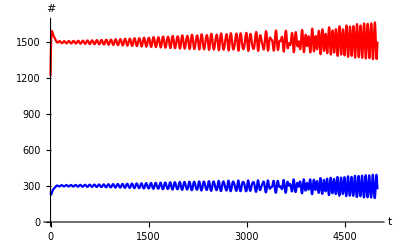

```mathematica
ListLinePlot[{Table[{t,Sum[ssol[h,t],{h,1,3}]},{t,0,tmax/.pars}],Table[{t,Sum[isol[h,p,t],{h,1,3},{p,1,3}]},{t,0,tmax/.pars}]},PlotStyle->{Red,Blue},AxesLabel->{"t","#"}]
```

#### Allele Frequency dynamics

Plotted over time

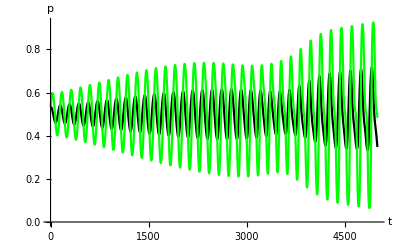

```mathematica
ListLinePlot[{Table[{t,(ssol[1,t]+1/2 ssol[2,t]+Sum[isol[1,p,t]+1/2 isol[2,p,t],{p,1,3}])/Sum[ssol[k,t]+Sum[isol[k,l,t],{l,1,3}],{k,1,3}]},{t,0,tmax/.pars}],Table[{t,Sum[isol[1,p,t]+1/2 isol[2,p,t],{p,1,3}]/Sum[isol[k,l,t],{l,1,3},{k,1,3}]},{t,0,tmax/.pars}]},PlotStyle->{Black,Green},PlotRange->All,AxesLabel->{"t","p"}]
```

Plotted in phase space (starting condition shown as a red point):

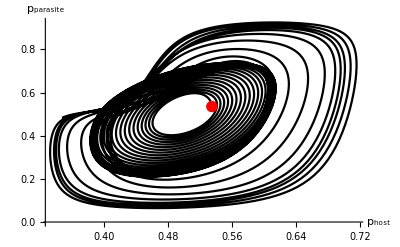

```mathematica
Show[ListLinePlot[{Table[{(ssol[1,t]+1/2 ssol[2,t]+Sum[isol[1,p,t]+1/2 isol[2,p,t],{p,1,3}])/Sum[ssol[k,t]+Sum[isol[k,l,t],{l,1,3}],{k,1,3}],Sum[isol[1,p,t]+1/2 isol[2,p,t],{p,1,3}]/Sum[isol[k,l,t],{l,1,3},{k,1,3}]},{t,0,tmax/.pars}]},PlotStyle->{Black},PlotRange->All,AxesLabel->{"p_host","p_parasite"}],
ListPlot[{{(ssol[1,0]+1/2 ssol[2,0]+Sum[isol[1,p,0]+1/2 isol[2,p,0],{p,1,3}])/Sum[ssol[k,0]+Sum[isol[k,l,0],{l,1,3}],{k,1,3}],Sum[isol[1,p,0]+1/2 isol[2,p,0],{p,1,3}]/Sum[isol[k,l,0],{l,1,3},{k,1,3}]}/.pars},PlotStyle->{PointSize[0.02],Red}]
]
```

## Numerical stability

### Jacobian matrix

```mathematica
nJmtrx[Pars_]:=Block[{jmtrx,out,h1,h2,p1,p2,row},jmtrx=Table[{},{row,1,12}];
For[h1=1,h1≤3,h1++,row=h1;
For[h2=1,h2≤3,h2++,
AppendTo[jmtrx[[row]],D[f1[h1,t],s[h2,t]]]
];
For[h2=1,h2≤3,h2++,
For[p2=1,p2≤3,p2++,
AppendTo[jmtrx[[row]],D[f1[h1,t],i[h2,p2,t]]]
];
];
];
For[h1=1,h1≤3,h1++,
For[p1=1,p1≤3,p1++,row=3+3(h1-1)+p1;
For[h2=1,h2≤3,h2++,
AppendTo[jmtrx[[row]],D[f2[h1,p1,t],s[h2,t]]];
];
For[h2=1,h2≤3,h2++,
For[p2=1,p2≤3,p2++,
AppendTo[jmtrx[[row]],D[f2[h1,p1,t],i[h2,p2,t]]]
];
];
];
];
jmtrx/.Pars/.nEqu[Pars]
]
```

```mathematica
Eigenvalues[nJmtrx[pars]]
```

{0.981813+0.0328329 ⅈ,0.981813-0.0328329 ⅈ,0.981813+0.0328329 ⅈ,0.981813-0.0328329 ⅈ,0.95+0. ⅈ,0.95+0. ⅈ,0.95+0. ⅈ,0.95+0. ⅈ,0.95+0. ⅈ,0.95+0. ⅈ,0.895901+0.0407836 ⅈ,0.895901-0.0407836 ⅈ}

### Stability function

```mathematica
stab[Pars_]:=Block[{λs,mag,out},
If[Length[nEqu[Pars]]<1,out=0 (*No endemic equilibrium*),
λs=Eigenvalues[nJmtrx[Pars]]//Chop;
mag=Sqrt[Re[λs]^2+Im[λs]^2];
If[Max[Im[λs]]>0,
(*Cycles*)If[Max[mag]>1,(*unstable*)out=3,(*stable*)out=2],
(*No cycles*)out=1] 
];
out
]
```

### Stability across parameter space

Here we explore the stability of the system as a function of the fertility upon infection, ρ, and virulence, μ, focusing solely on the disease-present equilibrium.

```mathematica
parsSub={r->0.2,κ->1/2000,β->0.0002,Δt->1};
```

```mathematica
tab1=Table[{x,10^y,stab[Join[parsSub,{ρ->x,μ->10^y}]]},{x,0,1,0.2},{y,-6,-1,1}];
```

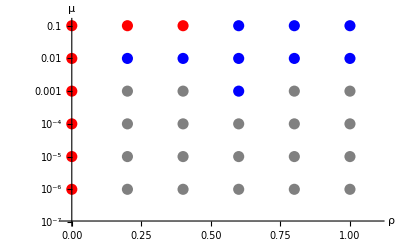

```mathematica
ListLogPlot[{Join[Select[Flatten[tab1,1],#[[3]]==0&][[;;,{1,2}]],{{-100,-100}}],Join[Select[Flatten[tab1,1],#[[3]]==1&][[;;,{1,2}]],{{-100,-100}}],
Join[Select[Flatten[tab1,1],#[[3]]==2&][[;;,{1,2}]],{{-100,-100}}],
Join[Select[Flatten[tab1,1],#[[3]]==3&][[;;,{1,2}]],{{-100,-100}}]},PlotRange->{{-0.02,1.1},{10^-7,10^-0.9}},AxesLabel->{"ρ","μ"},PlotStyle-> {{PointSize[0.02],Black},{PointSize[0.02],Gray},{PointSize[0.02],Blue},{PointSize[0.02],Red}}]
```

Black = No equilibrium with disease present
Gray = No cycles (leading eigenvalue is real)
Blue = Stable endemic equilibrium with damped cycles. Allele-frequency cycles, if present, dissipate.
Red = Unstable equilibrium with cycles. Possible allele-frequency limit cycles.

Plotting ρ on a log scale to focus on parameters with high levels of castration (ρ near zero):

```mathematica
tab2=Table[{10^x,10^y,stab[Join[parsSub,{ρ->10^x,μ->10^y}]]},{x,-4,Log10[0.3],0.2},{y,-3,-0.5,0.5}];
```

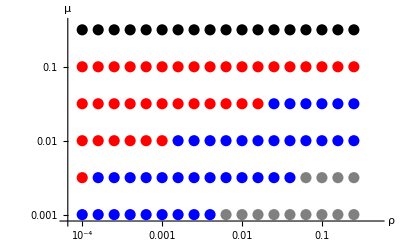

```mathematica
ListLogLogPlot[{Join[Select[Flatten[tab2,1],#[[3]]==0&][[;;,{1,2}]],{{-100,-100}}],Join[Select[Flatten[tab2,1],#[[3]]==1&][[;;,{1,2}]],{{-100,-100}}],
Join[Select[Flatten[tab2,1],#[[3]]==2&][[;;,{1,2}]],{{-100,-100}}],
Join[Select[Flatten[tab2,1],#[[3]]==3&][[;;,{1,2}]],{{-100,-100}}]},PlotRange->{{10^-4.2,0.5},{10^-3.1,10^-0.4}},AxesLabel->{"ρ","μ"},PlotStyle-> {{PointSize[0.02],Black},{PointSize[0.02],Gray},{PointSize[0.02],Blue},{PointSize[0.02],Red}}]
```

Black = No equilibrium with disease present
Gray = No cycles (leading eigenvalue is real)
Blue = Stable endemic equilibrium with damped cycles. Allele-frequency cycles, if present, dissipate.
Red = Unstable equilibrium with cycles. Possible allele-frequency limit cycles.

### Checking for allele frequency cycles

In the previous section red points denoted parameter combinations with a leading positive complex eigenvalue and hence possible exhibit allele frequency limit cycles.  Here we assess whether these points do likely have allele frequency limit or stable cycles by calculating whether the variance in allele frequency increases or decreases over time.

```mathematica
AFstab[ρμPt_]:=Block[{j,ρ,μ,Pars,vH1,vH2,vP1,vP2,out}, 
Clear[ssol,isol];
Pars=Join[parsSub,{ρ->ρμPt[[1]], μ->ρμPt[[2]],tmax->5000 }];out={};
nsol=nIterate[Pars];
ssol[h_,t_]:=nsol[[t+1,h]];
isol[h_,p_,t_]:=nsol[[t+1,3+3(h-1)+p]];
(*Comparing variance between interval t=[0,1000] vs. interval t=[4000,5000]*)
vH1=Variance[Table[(ssol[1,t]+1/2 ssol[2,t]+Sum[isol[1,p,t]+1/2 isol[2,p,t],{p,1,3}])/Sum[ssol[k,t]+Sum[isol[k,l,t],{l,1,3}],{k,1,3}],{t,0,1000}]];
vH2=Variance[Table[(ssol[1,t]+1/2 ssol[2,t]+Sum[isol[1,p,t]+1/2 isol[2,p,t],{p,1,3}])/Sum[ssol[k,t]+Sum[isol[k,l,t],{l,1,3}],{k,1,3}],{t,4000,5000}]];
vP1=Variance[Table[Sum[isol[1,p,t]+1/2 isol[2,p,t],{p,1,3}]/Sum[isol[k,l,t],{l,1,3},{k,1,3}],{t,0,1000}]];
vP2=Variance[Table[Sum[isol[1,p,t]+1/2 isol[2,p,t],{p,1,3}]/Sum[isol[k,l,t],{l,1,3},{k,1,3}],{t,4000,5000}]];
If[vH1>vH2,
(*host stable*)
If[vP1>vP2,(*parasite stable*)out={1,vH2-vH1,vP2-vP1},(*parasite unstable=Error*) out={3,vH2-vH1,vP2-vP1}],
(*host unstable*)
If[vP1>vP2,(*parasite stable=Error*)out={3,vH2-vH1,vP2-vP1},(*parasite unstable*) out={2,vH2-vH1,vP2-vP1}]];
out
]
```

If AFstab={1,-,-} then stable allele frequency cycles
If AFstab={2,+,+} then unstable allele frequency cycles
If AFstab={3,+,-} or {3,-,+} then host and parasite variance trends do not agree. Possible problem with length of intervals relative to period of cycles.

For each red point in tab2 are there likely allele frequency cycles?

```mathematica
Module[{j,Pts},Cycles2={};
Pts=Select[Flatten[tab2,1],#[[3]]==3&][[;;,{1,2}]];
For[j=1,j≤Length[Pts],j++,
AppendTo[Cycles2,Join[Pts[[j]],{AFstab[Pts[[j]]]}]]
];
]
```

```mathematica
Cycles2
```

{{0.0001,0.00316228,{2,0.0109266,0.0554364}},{0.0001,0.01,{2,0.00901662,0.0502833}},{0.0001,0.0316228,{2,0.00901893,0.0486751}},{0.0001,0.1,{2,0.0130479,0.0649044}},{0.000158489,0.01,{2,0.00901522,0.0502782}},{0.000158489,0.0316228,{2,0.00901878,0.0486737}},{0.000158489,0.1,{2,0.0130479,0.0649043}},{0.000251189,0.01,{2,0.009013,0.05027}},{0.000251189,0.0316228,{2,0.00901853,0.0486715}},{0.000251189,0.1,{2,0.0130478,0.0649041}},{0.000398107,0.01,{2,0.0090095,0.0502571}},{0.000398107,0.0316228,{2,0.00901815,0.048668}},{0.000398107,0.1,{2,0.0130478,0.0649038}},{0.000630957,0.01,{2,0.00900397,0.0502367}},{0.000630957,0.0316228,{2,0.00901753,0.0486625}},{0.000630957,0.1,{2,0.0130477,0.0649033}},{0.001,0.01,{2,0.00899526,0.0502042}},{0.001,0.0316228,{2,0.00901656,0.0486537}},{0.001,0.1,{2,0.0130476,0.0649026}},{0.00158489,0.0316228,{2,0.00901503,0.0486398}},{0.00158489,0.1,{2,0.0130475,0.0649015}},{0.00251189,0.0316228,{2,0.0090126,0.0486178}},{0.00251189,0.1,{2,0.0130472,0.0648997}},{0.00398107,0.0316228,{2,0.00900876,0.0485833}},{0.00398107,0.1,{2,0.0130468,0.0648969}},{0.00630957,0.0316228,{2,0.00900271,0.048529}},{0.00630957,0.1,{2,0.0130461,0.0648924}},{0.01,0.0316228,{2,0.00899319,0.0484442}},{0.01,0.1,{2,0.0130451,0.0648853}},{0.0158489,0.0316228,{2,0.00897827,0.048313}},{0.0158489,0.1,{2,0.0130435,0.064874}},{0.0251189,0.1,{2,0.0130409,0.0648562}},{0.0398107,0.1,{2,0.0130367,0.064828}},{0.0630957,0.1,{2,0.0130302,0.0647835}},{0.1,0.1,{2,0.01302,0.0647132}},{0.158489,0.1,{2,0.0130038,0.0646025}},{0.251189,0.1,{2,0.0129785,0.0644292}}}

All red points appear to have allele frequency limit cycles.

Conclusion: The disease-present equilibrium is unstable, with perturbations cycling outwards, only when the disease reduces fertility severely (ρ near 0) or has a high mortality cost (μ high) or both.

## Continuous-time SI model with asexual hosts and parasites

Similar model but with asexual hosts and parasites.

The differential equations

Let s[h,t] be the number of susceptible hosts of genotype h at time t and i[h,p,t] the number of infected hosts of type h infected with pathogen of genotype p. Here h and p range from 1 to 3 representing a diploid genotype at a single locus. Hosts and pathogens produce sexually with all offspring entering the susceptible class.  If we let n be a vector of length 3 giving the number of viable parents of each genotype the number of offspring of type j produced by random mating is given by:

Letting ds[h,t]/dt=g1[h,t] and di[h,p,t]/dt=g2[h,p,t]

```mathematica
Clear[g1,g2]
```

```mathematica
lm={{1,0,0},{0,1,0},{0,0,1}};
g1[h_,t_]:=r(1-κ (Sum[s[k,t]+Sum[i[k,p,t],{p,1,3}],{k,1,3}])) (s[h,t]+ρ Sum[i[h,p,t],{p,1,3}])-β s[h,t]Sum[lm[[h,l]] i[k,l,t],{k,1,3},{l,1,3}]
g2[h_,p_,t_]:=β s[h,t]Sum[lm[[h,p]] i[k,p,t],{k,1,3}]-μ i[h,p,t]
```

Here r is the growth rate, κ is the inverse of the carrying capacity, ρ is the fertility of infected hosts with 0 being complete castration and 1 being no fertility cost, β is the transmission rate, and μ is the virulent death rate of infected hosts.

Numerical Analysis

```mathematica
pars={r->0.2,κ->1/2000,ρ->1,β->0.0002,μ->0.05,tmax->5000};
```

## The equilibria

```mathematica
equs=Join[Table[g1[h,t]==0,{h,1,3}],Flatten[Table[g2[h,p,t]==0,{h,1,3},{p,1,3}]]];
vars=Join[Table[s[h,t],{h,1,3}],Flatten[Table[i[h,p,t],{h,1,3},{p,1,3}]]];
```

```mathematica
nEqu[Pars_]:=Block[{nsol,out},
nsol=Solve[equs/.Pars,vars]//Quiet;
out=Select[nsol,(s[1,t]/.#)>0&&(s[2,t]/.#)>0&&(s[3,t]/.#)>0&&(i[1,1,t]/.#)>0&]//Flatten
]
```

```mathematica
nEqu[pars]
```

{s[1,t]→250.,s[2,t]→250.,s[3,t]→250.,i[1,1,t]→322.749,i[1,2,t]→0.,i[1,3,t]→0.,i[2,1,t]→0.,i[2,2,t]→322.749,i[2,3,t]→0.,i[3,1,t]→0.,i[3,2,t]→0.,i[3,3,t]→322.749}

## Numerical Simulation

### Numerical Iteration

```mathematica
Clear[ssol,isol,nsol]
```

The equations

```mathematica
ODEs=Join[Table[D[s[h,t],t]==g1[h,t],{h,1,3}],Flatten[Table[D[i[h,p,t],t]==g2[h,p,t],{h,1,3},{p,1,3}]]];
vars=Join[Table[s[h,t],{h,1,3}],Flatten[Table[i[h,p,t],{h,1,3},{p,1,3}]]];
```

The inital conditions

```mathematica
equ=nEqu[pars];
```

```mathematica
inits=Join[Table[s[h,0]==0.9^h s[h,t]/.equ,{h,1,3}],Flatten[Table[i[h,p,0]==0.9^h i[h,p,t]/.equ,{h,1,3},{p,1,3}]]]
```

{s[1,0]==225.,s[2,0]==202.5,s[3,0]==182.25,i[1,1,0]==290.474,i[1,2,0]==0.,i[1,3,0]==0.,i[2,1,0]==0.,i[2,2,0]==261.426,i[2,3,0]==0.,i[3,1,0]==0.,i[3,2,0]==0.,i[3,3,0]==235.284}

Numerically integrating

```mathematica
nsol=NDSolve[Join[ODEs/.pars,inits],vars,{t,0,tmax/.pars}]//Flatten;
ssol[h_,τ_]:=s[h,t]/.nsol/.{t->τ}
isol[h_,p_,τ_]:=i[h,p,t]/.nsol/.{t->τ}
```

### Numerical Iteration

Numerical iteration as a function of parameter combination

```mathematica
nIterate[Pars_]:=Block[{ODEs,vars,ssol,isol,nsol,out,equ},
Clear[ssol,isol,nsol];
(*The equations*)
ODEs=Join[Table[D[s[h,t],t]==g1[h,t],{h,1,3}],Flatten[Table[D[i[h,p,t],t]==g2[h,p,t],{h,1,3},{p,1,3}]]];
vars=Join[Table[s[h,t],{h,1,3}],Flatten[Table[i[h,p,t],{h,1,3},{p,1,3}]]];
(*Inital conditions*)
equ=nEqu[Pars];
inits=Join[Table[s[h,0]==0.9^h s[h,t]/.equ,{h,1,3}],Flatten[Table[i[h,p,0]==0.9^h i[h,p,t]/.equ,{h,1,3},{p,1,3}]]];
(*Itterating*)
out=NDSolve[Join[ODEs/.Pars,inits],vars,{t,0,tmax/.Pars}]//Flatten
]
```

```mathematica
Clear[ssol,isol,nsol]
```

```mathematica
nsol=nIterate[pars];
ssol[h_,τ_]:=s[h,t]/.nsol/.{t->τ}
isol[h_,p_,τ_]:=i[h,p,t]/.nsol/.{t->τ}
```

### Plotting

#### Epidemiological dynamics

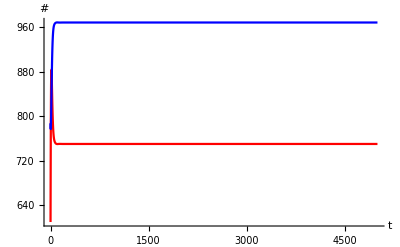

```mathematica
ListLinePlot[{Table[{t,Sum[ssol[h,t],{h,1,3}]},{t,0,tmax/.pars}],Table[{t,Sum[isol[h,p,t],{h,1,3},{p,1,3}]},{t,0,tmax/.pars}]},PlotStyle->{Red,Blue},AxesLabel->{"t","#"}]
```

#### Allele Frequency dynamics

Plotted over time

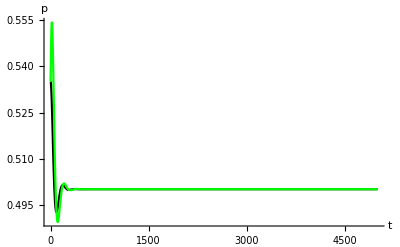

```mathematica
ListLinePlot[{Table[{t,(ssol[1,t]+1/2 ssol[2,t]+Sum[isol[1,p,t]+1/2 isol[2,p,t],{p,1,3}])/Sum[ssol[k,t]+Sum[isol[k,l,t],{l,1,3}],{k,1,3}]},{t,0,tmax/.pars}],Table[{t,Sum[isol[1,p,t]+1/2 isol[2,p,t],{p,1,3}]/Sum[isol[k,l,t],{l,1,3},{k,1,3}]},{t,0,tmax/.pars}]},PlotStyle->{Black,Green},PlotRange->All,AxesLabel->{"t","p"}]
```

Plotted in phase space (starting condition shown as a red point):

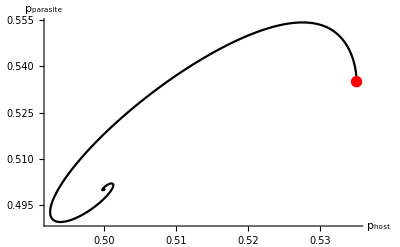

```mathematica
Show[ListLinePlot[{Table[{(ssol[1,t]+1/2 ssol[2,t]+Sum[isol[1,p,t]+1/2 isol[2,p,t],{p,1,3}])/Sum[ssol[k,t]+Sum[isol[k,l,t],{l,1,3}],{k,1,3}],Sum[isol[1,p,t]+1/2 isol[2,p,t],{p,1,3}]/Sum[isol[k,l,t],{l,1,3},{k,1,3}]},{t,0,tmax/.pars}]},PlotStyle->{Black},PlotRange->All,AxesLabel->{"p_host","p_parasite"}],
ListPlot[{{(ssol[1,0]+1/2 ssol[2,0]+Sum[isol[1,p,0]+1/2 isol[2,p,0],{p,1,3}])/Sum[ssol[k,0]+Sum[isol[k,l,0],{l,1,3}],{k,1,3}],Sum[isol[1,p,0]+1/2 isol[2,p,0],{p,1,3}]/Sum[isol[k,l,0],{l,1,3},{k,1,3}]}/.pars},PlotStyle->{PointSize[0.02],Red}]
]
```

## Numerical stability

### Jacobian matrix

```mathematica
nJmtrx[Pars_]:=Block[{jmtrx,out,h1,h2,p1,p2,row},jmtrx=Table[{},{row,1,12}];
For[h1=1,h1≤3,h1++,row=h1;
For[h2=1,h2≤3,h2++,
AppendTo[jmtrx[[row]],D[g1[h1,t],s[h2,t]]]
];
For[h2=1,h2≤3,h2++,
For[p2=1,p2≤3,p2++,
AppendTo[jmtrx[[row]],D[g1[h1,t],i[h2,p2,t]]]
];
];
];
For[h1=1,h1≤3,h1++,
For[p1=1,p1≤3,p1++,row=3+3(h1-1)+p1;
For[h2=1,h2≤3,h2++,
AppendTo[jmtrx[[row]],D[g2[h1,p1,t],s[h2,t]]];
];
For[h2=1,h2≤3,h2++,
For[p2=1,p2≤3,p2++,
AppendTo[jmtrx[[row]],D[g2[h1,p1,t],i[h2,p2,t]]]
];
];
];
];
jmtrx/.Pars/.nEqu[Pars]
]
```

```mathematica
Eigenvalues[nJmtrx[pars]]
```

{-0.104099+0.0407836 ⅈ,-0.104099-0.0407836 ⅈ,-0.05+0. ⅈ,-0.05+0. ⅈ,-0.05+0. ⅈ,-0.05+0. ⅈ,-0.05+0. ⅈ,-0.05+0. ⅈ,-0.0181872+0.0328329 ⅈ,-0.0181872-0.0328329 ⅈ,-0.0181872+0.0328329 ⅈ,-0.0181872-0.0328329 ⅈ}

### Stability function

```mathematica
stab[Pars_]:=Block[{λs,mag,out},
If[Length[nEqu[Pars]]<1,out=0 (*No endemic equilibrium*),
λs=Eigenvalues[nJmtrx[Pars]]//Chop;
If[Max[Im[λs]]>0,
(*Cycles*)If[Max[Re[λs]]>0,(*unstable*)out=3,(*stable*)out=2],
(*No cycles*)out=1] 
];
out
]
```

### Stability across parameter space

Here we explore the stability of the system as a function of the fertility upon infection, ρ, and virulence, μ, focusing solely on the disease-present equilibrium.

```mathematica
parsSub={r->0.2,κ->1/2000,β->0.0002};
```

```mathematica
tab1=Table[{x,10^y,stab[Join[parsSub,{ρ->x,μ->10^y}]]},{x,0,1,0.2},{y,-6,-1,1}];
```

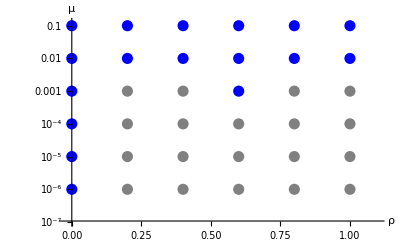

```mathematica
ListLogPlot[{Join[Select[Flatten[tab1,1],#[[3]]==0&][[;;,{1,2}]],{{-100,-100}}],Join[Select[Flatten[tab1,1],#[[3]]==1&][[;;,{1,2}]],{{-100,-100}}],
Join[Select[Flatten[tab1,1],#[[3]]==2&][[;;,{1,2}]],{{-100,-100}}],
Join[Select[Flatten[tab1,1],#[[3]]==3&][[;;,{1,2}]],{{-100,-100}}]},PlotRange->{{-0.02,1.1},{10^-7,10^-0.9}},AxesLabel->{"ρ","μ"},PlotStyle-> {{PointSize[0.02],Black},{PointSize[0.02],Gray},{PointSize[0.02],Blue},{PointSize[0.02],Red}}]
```

Black = No equilibrium with disease present
Gray = No cycles (leading eigenvalue is real)
Blue = Stable endemic equilibrium with damped cycles. Allele-frequency cycles, if present, dissipate.
Red = Unstable equilibrium with cycles. Possible allele-frequency limit cycles.

Plotting ρ on a log scale to focus on parameters with high levels of castration (ρ near zero):

```mathematica
tab2=Table[{10^x,10^y,stab[Join[parsSub,{ρ->10^x,μ->10^y}]]},{x,-4,Log10[0.3],0.2},{y,-3,-0.5,0.5}];
```

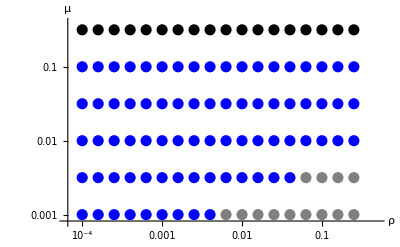

```mathematica
ListLogLogPlot[{Join[Select[Flatten[tab2,1],#[[3]]==0&][[;;,{1,2}]],{{-100,-100}}],Join[Select[Flatten[tab2,1],#[[3]]==1&][[;;,{1,2}]],{{-100,-100}}],
Join[Select[Flatten[tab2,1],#[[3]]==2&][[;;,{1,2}]],{{-100,-100}}],
Join[Select[Flatten[tab2,1],#[[3]]==3&][[;;,{1,2}]],{{-100,-100}}]},PlotRange->{{10^-4.2,0.5},{10^-3.1,10^-0.4}},AxesLabel->{"ρ","μ"},PlotStyle-> {{PointSize[0.02],Black},{PointSize[0.02],Gray},{PointSize[0.02],Blue},{PointSize[0.02],Red}}]
```

Black = No equilibrium with disease present
Gray = No cycles (leading eigenvalue is real)
Blue = Stable endemic equilibrium with damped cycles. Allele-frequency cycles, if present, dissipate.
Red = Unstable equilibrium with cycles. Possible allele-frequency limit cycles.

### Checking for allele frequency cycles

Once again checking red points for allele frequency limit cycles.

```mathematica
AFstab[ρμPt_]:=Block[{j,ρ,μ,Pars,vH1,vH2,vP1,vP2,out}, 
Clear[ssol,isol];
Pars=Join[parsSub,{ρ->ρμPt[[1]], μ->ρμPt[[2]],tmax->5000 }];out={};
nsol=nIterate[pars];
ssol[h_,τ_]:=s[h,t]/.nsol/.{t->τ};
isol[h_,p_,τ_]:=i[h,p,t]/.nsol/.{t->τ};
(*Comparing variance between interval t=[0,1000] vs. interval t=[4000,5000]*)
vH1=Variance[Table[(ssol[1,t]+1/2 ssol[2,t]+Sum[isol[1,p,t]+1/2 isol[2,p,t],{p,1,3}])/Sum[ssol[k,t]+Sum[isol[k,l,t],{l,1,3}],{k,1,3}],{t,0,1000}]];
vH2=Variance[Table[(ssol[1,t]+1/2 ssol[2,t]+Sum[isol[1,p,t]+1/2 isol[2,p,t],{p,1,3}])/Sum[ssol[k,t]+Sum[isol[k,l,t],{l,1,3}],{k,1,3}],{t,4000,5000}]];
vP1=Variance[Table[Sum[isol[1,p,t]+1/2 isol[2,p,t],{p,1,3}]/Sum[isol[k,l,t],{l,1,3},{k,1,3}],{t,0,1000}]];
vP2=Variance[Table[Sum[isol[1,p,t]+1/2 isol[2,p,t],{p,1,3}]/Sum[isol[k,l,t],{l,1,3},{k,1,3}],{t,4000,5000}]];
If[vH1>vH2,
(*host stable*)
If[vP1>vP2,(*parasite stable*)out={1,vH2-vH1,vP2-vP1},(*parasite unstable=Error*) out={3,vH2-vH1,vP2-vP1}],
(*host unstable*)
If[vP1>vP2,(*parasite stable=Error*)out={3,vH2-vH1,vP2-vP1},(*parasite unstable*) out={2,vH2-vH1,vP2-vP1}]];
out
]
```

If AFstab={1,-,-} then stable allele frequency cycles
If AFstab={2,+,+} then unstable allele frequency cycles
If AFstab={3,+,-} or {3,-,+} then host and parasite variance trends do not agree. Possible problem with length of intervals relative to period of cycles.

For each red point in tab2 are there likely allele frequency cycles?

```mathematica
Module[{j,Pts},Cycles2={};
Pts=Select[Flatten[tab2,1],#[[3]]==3&][[;;,{1,2}]];
For[j=1,j≤Length[Pts],j++,
AppendTo[Cycles2,Join[Pts[[j]],{AFstab[Pts[[j]]]}]]
];
]
```

```mathematica
Cycles2
```

{}

There are no red points

Conclusion: The disease-present equilibrium is no longer unstable, with perturbations cycling outwards, when the host and parasite reproduce asexually.